# Fibbinary

Fibbinary[n]
gives the nth fibbinary number. 
   Fibbinary[{n}]
gives a list of fibbinary numbers less than or equal to n.

Fibbinary numbers are the positive integers whose binary representation contains no consecutive ones.

## See AlsoSeeAlsoInsert links to any related reference (function) pages.

"XXXX" ▪

## Tech NotesTechNotesInsert links to related tech notes.

## Related Guides

## Related LinksRelatedLinksInsert links to any related page, including web pages.

## Examples InitializationExamplesInitializationInput that is to be evaluated before any examples are run, e.g. Needs[…].

```mathematica
Needs["PeterBurbery`CombinatoricsPaclet`"]
```

## Basic Examples | More Examples ⊳

First one hundred fibbinaries:

```mathematica
Table[Fibbinary[n],{n,100}]
```

{1,2,4,5,8,9,10,16,17,18,20,21,32,33,34,36,37,40,41,42,64,65,66,68,69,72,73,74,80,81,82,84,85,128,129,130,132,133,136,137,138,144,145,146,148,149,160,161,162,164,165,168,169,170,256,257,258,260,261,264,265,266,272,273,274,276,277,288,289,290,292,293,296,297,298,320,321,322,324,325,328,329,330,336,337,338,340,341,512,513,514,516,517,520,521,522,528,529,530,532}

Fibbinaries less than or equal to 50, represented in base 2:

```mathematica
BaseForm[#,2]&/@Fibbinary[{50}]//Column
```

1_2
10_2
100_2
101_2
1000_2
1001_2
1010_2
10000_2
10001_2
10010_2
10100_2
10101_2
100000_2
100001_2
100010_2
100100_2
100101_2
101000_2
101001_2
101010_2

Plot of fibbinaries less than 150 in base 2:

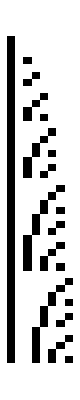

```mathematica
IntegerDigits[Fibbinary[{150}],2]//ArrayPlot
```

## More ExamplesMoreExamplesExtended examples in standardized sections.

### Scope

### Generalizations & Extensions

### Options

### Applications

### Properties & Relations

Fibbinaries are related to the Zeckendorf representation:

```mathematica
Fibbinary[12]
```

21

```mathematica
IntegerDigits[Fibbinary[12],2]
```

{1,0,1,0,1}

```mathematica
ZeckendorfRepresentation[12]
```

{1,0,1,0,1}

Adding the following integers gives 12:

```mathematica
Pick[Fibonacci[Range[2,6]],{1,0,1,0,1},1]
```

{1,3,8}

```mathematica
Total[%]
```

12

### Possible Issues

### Interactive Examples

### Neat Examples

## Metadata

### CategorizationMetadataMetadata such as page URI, context, and type of documentation page.

Symbol

PeterBurbery/CombinatoricsPaclet

PeterBurbery`CombinatoricsPaclet`

PeterBurbery/CombinatoricsPaclet/ref/Fibbinary

### Keywords

### Syntax Templates